## Harmonic Oscillator Redux

## Completed and Analyzed in class, April 8, 2025

This is the seventeenth notebook for you to finish in class. We are going to revisit the harmonic oscillator problems we solved back in the fourth and fifth notebooks. This time we are going to let Mathematica do all the hard work!

We are leaving behind the crutch of thinking of continuous systems as chunks. We are going to describe continuous systems as continuous systems, which means imagining the limit that the sizes of the chunks goes to zero while the number of chunks goes to infinity.

But first, we need to get familiar with how Mathematica expects continuous systems to be described. Just as we divided space into chunks, even before that in the course, we began by dividing time into steps and then used Euler’s Method or Second-Order Runge-Kutta to march forward through the discrete steps of time. In reality, probably all the way down to the unfathomably short amount of time (10^-43 seconds) known as the “Planck time,” time is also continuous.

Let’s see how we describe time-dependent differential equations to Mathematica. Before we get to guitar strings and drumheads, we are going all the way back to the problems we solved in the fourth and fifth notebooks, the damped and driven harmonic oscillator.

### Damped Harmonic Oscillator — Refresher

Back in the fourth notebook, we considered this force law:

F=-20x-v

We combined this with Newton’s Law F=ma with m=5 and then we had

5a=-20x-v

Then we got slightly fancier and more general. First we divided through by the 5 (whoop-do-doo — one step at a time). We  could also put all the terms on the left:

a+1/5 v+20/5 x=0

The ratio 20/5 is the ratio of the spring constant to the mass and we called that ω_0^2. So for these constants, ω_0=√(20/5)=2. The ratio1/5 is the ratio of the damping coefficient to the mass and we called that combination 2γ. So for these constants 2γ=1/5 or γ=1/10.

Our equation is now:

a+2γv+ω_0^2 x=0

When ω_0>γ as it is here (2 is definitely greater than 1/10), the system is “underdamped.” The greater the ratio of ω_0/γ the more oscillations occur for each  1/e-folding of the envelope of the oscillation as its motion damps toward nothing. We went through all this almost two months ago (in weeks three and four of the semester), and I am giving you a quick refresher. It is ok if you don’t remember all the harmonic oscillator results, because now we want to rediscover them, but by forcing Mathematica to do the hard work of breaking time into steps and applying its solvers.

### Derivatives and Their Notation

We have one more step, which is to introduce the notation of derivatives. We can’t tell Mathematica what to do if we don’t have a precise notation.

Recall that the velocity v is the rate of change (with respect to time) of the position x. Meanwhile the acceleration a is the rate of change (with respect to time) of the velocity v. The rate of change is called the derivative. To say that you want to take a derivative of x(t) with respect to t in Mathematica, you write:

```mathematica
Derivative[1][x][t];
```

Perhaps it is a bit clumsy, and indeed there are shorthands, but let us understand this form, because it is unambiguous and it is general which makes it powerful.

Derivative[1][x][t] says take one derivative of the function x with respect to its argument, and evaluate the resulting function at time t.

So far we haven’t done anything at all with our symbolic expression of the derivative. One thing we can do with it is just display it in a pretty form:

```mathematica
Derivative[1][x][t] // TraditionalForm
```

x'(t)

The afterthought of TraditionalForm says that you would like to see the result as it would be likely to be typeset in a mathematics textbook or in some physics textbooks. Note that physicists (and older mathematicians) often use a different notation for the derivatives. The notation is known as Leibniz notation. We have our hands full learning Mathematica’s notations. Let’s not add Leibniz notation into the mix we are already considering in this notebook.

The acceleration is the rate of change of the velocity, and that is the second derivative, and here is how you tell Mathematica you want to take a second derivative of x with respect to t:

```mathematica
Derivative[2][x][t] // TraditionalForm
```

x''(t)

### The Damped Oscillator Differential Equation

Here is how you write the whole damped oscillator equation (which if you scroll up, you will see we had whittled down to a+2γv+ω_0^2 x=0) in a way that Mathematica can unambiguously understand it, and as an afterthought, display it prettily:

```mathematica
Derivative[2][x][t]+2gamma Derivative[1][x][t]+omega0^2 x[t]==0 // TraditionalForm
```

2 gamma x'(t)+omega0^2 x(t)+x''(t)==0

Equations involving derivatives are called “differential equations.”

Notice with your full attention the use of == rather than = in the differential equation. We are not making an assignment! We are setting up a conditional test between two sides of an equation, and Mathematica is going to do its best to approximately satisfy that conditional test when (deep under the hood) it applies some differential-equation solving strategy like Euler, or Runge-Kutta Second Order, or maybe Runge-Kutta Fourth Order. (BTW, I apologize that I never got around to introducing Runge-Kutta Fourth Order as promised early in the course. It is a mess, even for me, and Runge-Kutta Second Order has been serving us fully satisfactorily.)

Now let’s also define omega0 and gamma for Mathematica, and also add some initial conditions on the position and velocity. Since we learned the Module notation recently, I’ll toss that in:

```mathematica
Module[{omega0=2, gamma=1/10},{Derivative[2][x][t]+2gamma Derivative[1][x][t]+omega0^2 x[t]==0,x[0]==0,Derivative[1][x][0]==3}] // TraditionalForm
```

{x''(t)+(x'(t))/5+4 x(t)==0,x(0)==0,x'(0)==3}

I set the initial position at t=0 as 0 and I set the initial velocity as 3. Again, it is extremely important to use == rather than = in the initial conditions as well as in the differential equation. We are setting up conditional tests and Mathematica is going to work to make them true. If you screw that up and put in assignments, it is quit and restart time.

We have failed to do one minor thing. We have set up a pile of equations, but we haven’t given them any name, so we can’t use them anywhere else without typing them in again.

Let’s give this pile of equations a name:

```mathematica
dampedOscillatorProblem=Module[{omega0=2, gamma=1/10},{Derivative[2][x][t]+2gamma Derivative[1][x][t]+omega0^2 x[t]==0,x[0]==0,Derivative[1][x][0]==3}] ;
```

### Making Mathematica Solve the Damped Harmonic Oscillator

This particular problem is exactly solvable. So you can tell Mathematica to try to exactly solve it using DSolve, and lo and behold, it succeeds:

```mathematica
DSolve[dampedOscillatorProblem]
```

{{x[t]→10 √(3/133) ⅇ^(-t/10) Sin[(√399 t)/10]}}

Notice that what is output is a list of lists of rules. All that generality is in case you have multiple functions being solved simultaneously.

We just have one function, so we grab the first and only list of rules out of the list of lists of rules:

```mathematica
dampedOscillatorSolutionRule = DSolve[dampedOscillatorProblem][[1]];
```

Display it so that we can see exactly what we got:

```mathematica
dampedOscillatorSolutionRule
```

{x[t]→10 √(3/133) ⅇ^(-t/10) Sin[(√399 t)/10]}

We still don’t have something we can plot, because you don’t plot a rule.

We have to turn the rule into a function, and we do that by first writing x[t] and then applying the rule to it:

```mathematica
x[t]/.dampedOscillatorSolutionRule
```

10 √(3/133) ⅇ^(-t/10) Sin[(√399 t)/10]

It isn’t particularly clumsy to write x[t]/.dampedOscillatorSolutionRule.

However, let’s be slicker and define a new function:

```mathematica
dampedOscillatorSolution[t_]=x[t]/.dampedOscillatorSolutionRule
```

10 √(3/133) ⅇ^(-t/10) Sin[(√399 t)/10]

To be frank, I don’t know why I might or might not use := above instead of =. I am following 
https://reference.wolfram.com/language/howto/SolveADifferentialEquation.html.en.

In that documentation they don’t use := so I am not. It definitely worked without the :=.

```mathematica
dampedOscillatorSolution[t]
```

10 √(3/133) ⅇ^(-t/10) Sin[(√399 t)/10]

Here is a screenshot of the relevant portion of the documentation. Maybe by the time we get done with EIWL3 I will understand why we are using = instead of := in this situation:

-Graphics-

### Plotting Damped Harmonic Motion

Finally, we plot the solution:

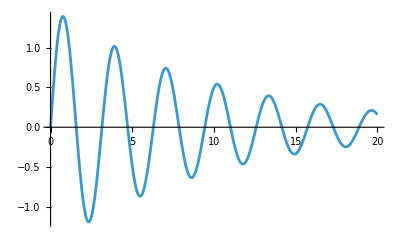

```mathematica
Plot[dampedOscillatorSolution[t],{t,0,20}]
```

### Animating Damped Harmonic Motion

We need a crude graphic:

```mathematica
oscillatorGraphic[displacement_, rectangleWidth_]:=Graphics[{
EdgeForm[Thin],White,
Rectangle[{-rectangleWidth/2,-rectangleWidth/4},{rectangleWidth/2,rectangleWidth/4}],
Black,
Point[{displacement,0}]
}]
```

In the above, rectangleWidth was a parameter, because the largest displacement is going to vary a lot from problem to problem. We want the displacement to not go outside the rectangle, and we will have to look at the solution and set rectangle width to be a little more than twice the maximum displacement.

Now we have something we can animate:

```mathematica
Animate[oscillatorGraphic[dampedOscillatorSolution[t],4],{t, 0, 20},DefaultDuration->20]
```

### Forced Harmonic Oscillator — Refresher

In the fifth notebook, we added a “driving” or “forcing” function to the oscillator. Our equation became:

a+2γv+ω_0^2 x=A/m sin ω_1 t

We chose A=100 (so with m=5, we have A/m=20) and ω_1 to be 1. Keep in mind that we have ω_0=2. Imagine that a kid on a swing swings naturally at some frequency, but you are pushing them repeatedly at half that frequency. The kid isn’t going to get very high. It is still an interesting place to start.

### Making Mathematica Solve the Forced Harmonic Oscillator

```mathematica
forcedOscillatorProblem=Module[{omega0=2, gamma=1/10,aoverm=20,omega1=1},{Derivative[2][x][t]+2gamma Derivative[1][x][t]+omega0^2 x[t]==aoverm Sin[omega1 t],x[0]==0,Derivative[1][x][0]==0}] ;
```

```mathematica
forcedOscillatorSolutionRule = DSolve[forcedOscillatorProblem][[1]];
```

```mathematica
forcedOscillatorSolution[t_]=x[t]/.forcedOscillatorSolutionRule
```

-(50 ⅇ^(-t/10) (399 ⅇ^(t/10) Cos[t]-399 Cos[(√399 t)/10]-5985 ⅇ^(t/10) Sin[t]+149 √399 Sin[(√399 t)/10]))/45087

### Plotting Forced Harmonic Motion

Finally, we plot the solution:

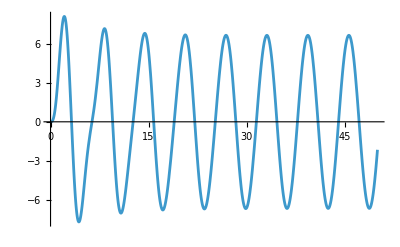

```mathematica
Plot[forcedOscillatorSolution[t],{t,0,50}]
```

### Animating Forced Harmonic Motion

```mathematica
Animate[oscillatorGraphic[forcedOscillatorSolution[t],100],{t, 0, 50},DefaultDuration->20]
```

### Forced Harmonic Oscillator — Resonance

The last thing we did in the fifth notebook, was to start messing with ω_1. We brought its value up just below the resonance value (we tried ω_1=1.8).  Then we went just above the resonance value (we tried ω_1=2.2).  We compared the notebook output to video of real systems:

https://youtu.be/aZNnwQ8HJHU.

Messing around with the value of ω_1 is begging us to introduce Manipulate[].

Mathematica has a bewildering number of guides on how to use DSolve. Fortunately for us, one of these covers combining DSolve[] and Manipulate[]:

https://reference.wolfram.com/language/howto/PlotTheResultsOfNDSolve.html.en

### Forced Harmonic Oscillator — Exploring Resonance With Manipulate

The recommended strategy in the guide referenced above is to put the entire problem to be solved inside the Manipulate function. Obviously this strategy is only going to work for problems that do not take long to solve or the Manipulate sliders are just going to feel terribly unresponsive.

Our problem with the changing resonance frequency requires one parameter, which I will imaginatively call “parameter ” and in Manipulate[] I will call it “p”:

```mathematica
resonanceProblem[parameter_]:=Module[{omega0=2, gamma=1/10,aoverm=20,omega1=parameter},{Derivative[2][x][t]+2gamma Derivative[1][x][t]+omega0^2 x[t]==aoverm Sin[omega1 t],x[0]==0,Derivative[1][x][0]==0}] ;
```

Be sure to stop the animations higher up in this document while operating the p-slider or your notebook will behave sluggishly.

Also, as you hold down and slide the p-slider 0.1 at a time, watch as Mathematica first displays a crude graphic, and then when you release the mouse, it cleans up the graphic by replacing it with a higher-precision calculation. Its use of discrete time steps leaks through while you are holding the slider, and then it takes some time to re-do the calculation with a larger number of time steps in the interval.

```mathematica
Manipulate[Plot[x[t]/.DSolve[resonanceProblem[p]][[1]]/.t->tPlot,{tPlot,0,50}, PlotRange->{{0,50},{-50,50}},PlotLabel->NumberForm[p,{2,1}]],{p,1.6,2.4,0.1}]
```

### Damped Harmonic Oscillator — Switching to NDSolve

Earlier in this notebook, we had Mathematica solve the damped harmonic oscillator. It is an exactly solvable problem. Mathematica did not need to break time up into steps. Of course, we can solve an exactly solvable problem with numerical methods. We use NDSolve[] instead of DSolve[].

First, let’s just have the problem handy again.

```mathematica
dampedOscillatorProblem=Module[{omega0=2, gamma=1/10},{Derivative[2][x][t]+2gamma Derivative[1][x][t]+omega0^2 x[t]==0,x[0]==0,Derivative[1][x][0]==3}] ;
```

Here is how you call NDSolve:

```mathematica
NDSolve[dampedOscillatorProblem,x,{t,0,20}];
```

The output is an interpolating function, and again it is a list of lists of rules. Take the first element of the list, convert the rule into a function, and give the result a name that we will shortly stick into Plot[]:

```mathematica
dampedOscillatorNumericalSolution[t_]=x[t]/.NDSolve[dampedOscillatorProblem,x,{t,0,20}][[1]]
```

InterpolatingFunction[…][t]

```mathematica
Plot[dampedOscillatorNumericalSolution[t],{t,0,20}]
```

-Graphics-

Compare this with the exact solution that we previously calculated and you’ll see that Mathematica has done well with its time steps and its approximate numerical solution:

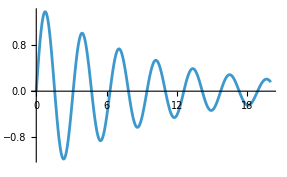

```mathematica
Plot[dampedOscillatorSolution[t],{t,0,20}]
```

For an even crisper comparison, we could put the two functions on the same plot:

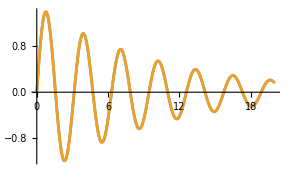

```mathematica
Plot[{dampedOscillatorNumericalSolution[t],dampedOscillatorSolution[t]},{t,0,20}]
```

The second function (in orange) perfectly covers up the first. You could make the second function thinner so it doesn’t completely cover up the first:

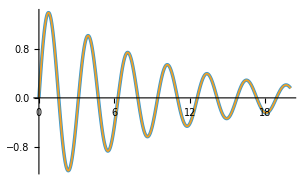

```mathematica
Plot[{dampedOscillatorNumericalSolution[t],dampedOscillatorSolution[t]},{t,0,20},PlotStyle->{Thickness[0.008],Thickness[0.004]}]
```

The bottom line is that whatever Mathematica is doing under the hood, its numerical solution is indistinguishable from its exact solution.

### Conclusion

This notebook has been a fairly complete survey of Mathematica’s tools for solving “ordinary” differential equations. Notice that we only have one object, the mass in the oscillator. We have not yet added the sophisticated continuum of objects that will yield waves. For that, we will need to go from ordinary differential equations to “partial” differential equations. In short, from one or more functions of t to one or more functions of t,x,y,and z.

Many problems that are of interest do not require partial differential equations. We are going to explore partial differential equations more to complete the promise of this course, but I’d encourage everyone to master the ordinary differential equation methods that we have just covered, because you will find those tremendously useful in field after field, from physics, to biology, to economics and high finance. Be slightly less concerned with mastering the partial differential equations material that comes in the remaining six classes. That stuff is primarily of use to physicists and engineers, although meteorologists, oceanographers, astrophysicists, chemists, and other scientists in physics-adjacent fields often have to delve deeply into partial differential equations too.

If you have learned how to apply DSolve[] and NDSolve[] to ordinary differential equations well enough to apply them to equations that appear in other fields, you could explore some other field, find some important problem in that field that is not exactly solvable, and explore its numerical solutions with NDSolve[]. This would make a good final project.

I had to do some subtle work to get the Manipulate[] working. You’ll need to study that code carefully if you want to do manipulations.

Animations are intuitive and necessary for those who can’t read graphs well. For final projects, I’d recommend creating high-quality graphs, and if you are going to use Manipulate[] use it to manipulate graphs, as I have above, rather than animations.